## Problem 2 (1.8.4)

We first confirm that u(x,t) is a solution of the KdV equation

```mathematica
v[x_,t_]=Log[1+Exp[k1*x-k1^3*t+α]+Exp[k2*x-k2^3*t+β]+((k1-k2)/(k1+k2))^2*Exp[k1*x-k1^3*t+α+k2*x-k2^3*t+β]];
```

```mathematica
u[x_,t_] = 12D[v[x,t],{x,2}];
```

If this evaluates to “True”, then u is indeed a solution.

```mathematica
FullSimplify[D[u[x,t],{t}]+u[x,t]*D[u[x,t],{x}]+D[u[x,t],{x,3}]]==0
```

True

```mathematica
α = 0; β = 1; (*Given values*)
```

### Part a

First, we plot the solution for some k_1/k_2>√3 .

```mathematica
k2 = 1; (*Normalize k2 to 1 so we only need to change k1*)
```

```mathematica
Animate[Plot[u[x,t]/.k1->2.1,{x,-20,20},PlotRange->{0,15},AxesLabel->{x,u}],{t,-10,10}]
```

Here, we observe two solitons, one of which is much taller and faster than the other. We see that the larger one initially follows the smaller one in moving in the positive x-direction before briefly encompassing entirely due to its faster movement. After this, the smaller one is left behind and the two continue to move at their respective velocities.

### Part b

Now, we consider two cases where √3>k_1/k_2>√((3+√5)/2) .

```mathematica
Animate[Plot[u[x,t]/.k1->1.72,{x,-20,20},PlotRange->{0,10},AxesLabel->{x,u}],{t,-10,10}]
```

```mathematica
Animate[Plot[u[x,t]/.k1->1.62,{x,-20,20},PlotRange->{0,10},AxesLabel->{x,u}],{t,-10,10}]
```

Now, we still see two distinct solitons, one of which is taller and faster than the other, but they now seem more distinct as one passes over the other. Rather than one “eating” the other during this overlap, they instead retain their individual shapes to some extent.

### Part c

Finally, we consider a case where  k_1/k_2<√((3+√5)/2) .

```mathematica
Animate[Plot[u[x,t]/.k1->1.4,{x,-20,20},PlotRange->{0,10},AxesLabel->{x,u}],{t,-10,10}]
```

Now, the solitons are much closer in speed and height, and their interaction is quite a bit different. Rather than one passing over the other, it appears that the higher height and speed of one is transferred to the other when they interact.

## Problem 4 (1.8.6)

### Part a

First, we experiment with the simpler solution from part a to help obtain the results presented in the pdf.

```mathematica
θ1[x_,t_]=1+α1*Exp[-k*x+ν1*k^2*t];
```

```mathematica
u1[x_,t_]=-2ν1*D[θ1[x,t],{x}]/θ1[x,t];
```

```mathematica
ν1 = -Pi; k = 1; α1 = Exp[1];
```

```mathematica
Animate[Plot[u1[x,t],{x,-20,20},PlotRange->{-10,10},AxesLabel->{x}],{t,-10,10}]
```

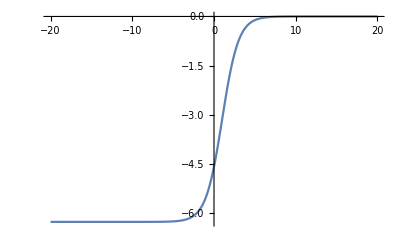

```mathematica
Plot[u1[x,0],{x,-20,20}]
```

### Part b

Now, we experiment with solution to Burgers equation from part b to try to find a pattern.

```mathematica
θ2[x_,t_]=1+α2*Exp[-K1*x+ν2*K1^2*t]+β2*Exp[-K2*x+ν2*K2^2*t];
```

```mathematica
u2[x_,t_]=-2*ν2*D[θ2[x,t],{x}]/θ2[x,t];
```

Based on the behavior we observed in part a, we expect that α and β will only shift our solution. Since ν is present in both terms, we should be able find the pattern by changing the ratio k_1/k_2 as in problem 2.

```mathematica
ν2 = Pi; K2 = 1; α2 = Exp[1]; β2 = Exp[-1]; K2=1;
```

```mathematica
Animate[Plot[u2[x,t]/.K1->-3,{x,-20,20},PlotRange->{-20,20},AxesLabel->{x}],{t,-10,10}]
```

First, in the case where k_1/k_2 is negative with large absolute value, we observe two waves in opposite spatial directions. One is much larger and faster than the other and appears to absorb it entirely and continue its quick movement upon collision.

```mathematica
Animate[Plot[u2[x,t]/.K1->-1.2,{x,-20,20},PlotRange->{-20,20},AxesLabel->{x}],{t,-10,10}]
```

When k_1/k_2 is closer to -1, we again see two waves in opposite spatial directions with one larger and faster, but upon their collision, they form a sigmoid-like shape like in part a which moves slowly in the direction that the larger wave was initially moving.

```mathematica
Animate[Plot[u2[x,t]/.K1->-1,{x,-20,20},PlotRange->{-20,20},AxesLabel->{x}],{t,-10,10}]
```

When k_1/k_2=-1, two waves in opposite spatial directions of equal speed and height collide and form a sigmoid-like shape which is completely stationary following the collision.

Note that for -1<k_1/k_2<0, we will essentially see the same results as those for k_1/k_2<-1 corresponding to k_2/k_1 but flipped in space and adjusted for α and β being different. The same logic also allows us to consider ignore the cases 0<k_1/k_2<1.

```mathematica
Animate[Plot[u2[x,t]/.K1->0,{x,-20,20},PlotRange->{-20,20},AxesLabel->{x}],{t,-10,10}]
```

When k_1=0, we essentially just observe the results from part a which makes since, because plugging in k_1=0 or k_2=0 eliminates the extra terms up to a scaling.

```mathematica
Animate[Plot[u2[x,t]/.K1->1,{x,-20,20},PlotRange->{-1,10},AxesLabel->{x}],{t,-10,10}]
```

For k_1/k_2=1, we also see a result which looks remarkably like that of part a. This again makes sense as  k_1=k_2 allows us to group the exponentials which produces a solution like that from part a but with different parameters.

```mathematica
Animate[Plot[u2[x,t]/.K1->1.2,{x,-50,10},PlotRange->{-1,10},AxesLabel->{x}],{t,-20,10}]
```

For k_1/k_2 close to 1, we see a slightly larger and faster wave overtake another. Note that we this occurs far in the negative x-direction and at an early time due to our choice of parameters.

```mathematica
Animate[Plot[u2[x,t]/.K1->3,{x,-50,10},PlotRange->{-1,30},AxesLabel->{x}],{t,-10,10}]
```

For large k_1/k_2, we can more clearly see a much larger and faster wave completely absorb the smaller and slower one and continue moving at its quick pace.